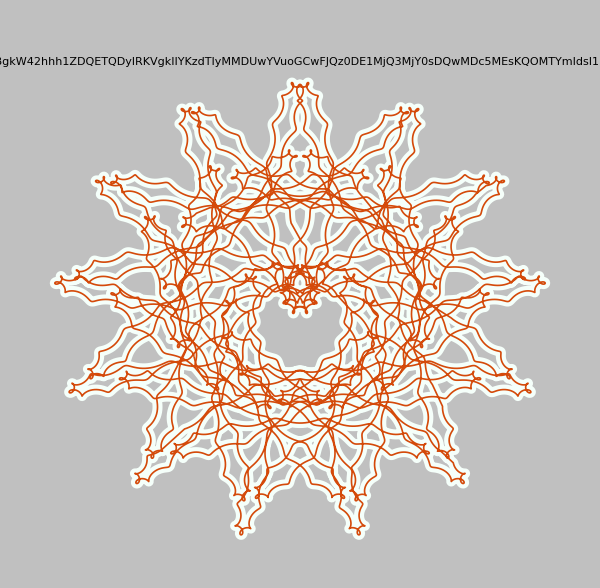

```mathematica
SF[a_,b_,c_,d_,t_]:={Sin[t/6]+a*Sin[b*t]Cos[t]+c*Sin[2^d*b *t],
Cos[t/6]+a Sin[b*t]*Sin[t]+c*Cos[16b*t]};
PSF[a_,b_,c_,d_]:=ParametricPlot[{SF[a,b,c,d,t],SF[a,b,c,d,t]},{t,0,12Pi},
PlotRange->All,Background->RGBColor["silver"],PlotPoints->200,
Axes->False,PlotLabel->{"a"->a,"b"->b,"c"->c,"d"->d},
PlotStyle->{{RGBColor["mintcream"],Thickness[.012]},
{RGBColor[RandomReal[.9,3]],Thickness[.002]}},ImageSize->600];
PSF[RandomReal[{.5,1.5}]*RandomChoice[{-1,1}],RandomInteger[{3,12}],
RandomReal[{.01,.1}]*RandomChoice[{-1,1}],RandomInteger[{3,6}]]
```

```mathematica
RRP[n_,o_,s_,c1_,c2_]:=Graphics[{FaceForm[Directive[RGBColor[c1],Opacity[.1o]]],
EdgeForm[Directive[RGBColor[c1],Opacity[.2o]]],
Polygon[ Outer[#1.#2 &,Table[RotationMatrix[a],{a,-Pi,Pi-Pi/o,Pi/o}],
Join[Map[ReflectionMatrix[{1,1}].# &,#],#]&@Join[{{0,0}},
RandomReal[{-1,1},{RandomInteger[{4,n}],2}]],1]]},
   Background->RGBColor[c2],ImageSize->s]
{RRP[32,3,300,"ghostwhite","steelblue"],RRP[16,4,300,RandomReal[1,3],"black"]}
```

{-Graphics-,-Graphics-}

```mathematica
RRP[32,3,600,RandomReal[1,3],"ghostwhite"]
```

-Graphics-

```mathematica
TP[n_,m_,s_,file_]:=Module[{img,rt},
img=Import[StringJoin["https://olgabelitskaya.github.io/",file]];
rt=RandomReal[{-1,1},{n,2}];
textpoly[x_]:={Opacity[RandomReal[{0.5, 0.7}]],EdgeForm[],Texture[img],
Polygon[x,VertexTextureCoordinates->x]};
Graphics[Rotate[textpoly[rt],#,{0, 0}]&/@Range[0,2 Pi,Pi/m],
ImageSize->s,Background->Black]];
{TP[32,3,300,"flower5.jpeg"],TP[24,6,300,"flower2.jpeg"]}
```

{-Graphics-,-Graphics-}

```mathematica
TP[64,5,600,"flower3.jpeg"]
```

-Graphics-

```mathematica
Multicolumn[ColorData["Gradients"],{9,6}]
```

AlpineColors | BrightBands | DeepSeaColors | LakeColors | Rainbow | StarryNightColors
Aquamarine | BrownCyanTones | FallColors | LightTemperatureMap | RedBlueTones | SunsetColors
ArmyColors | CandyColors | FruitPunchColors | LightTerrain | RedGreenSplit | TemperatureMap
AtlanticColors | CherryTones | FuchsiaTones | MintColors | RoseColors | ThermometerColors
AuroraColors | CMYKColors | GrayTones | NeonColors | RustTones | ValentineTones
AvocadoColors | CoffeeTones | GrayYellowTones | Pastel | SandyTerrain | WatermelonColors
BeachColors | DarkBands | GreenBrownTerrain | PearlColors | SiennaTones | 
BlueGreenYellow | DarkRainbow | GreenPinkTones | PigeonTones | SolarColors | 
BrassTones | DarkTerrain | IslandColors | PlumColors | SouthwestColors |

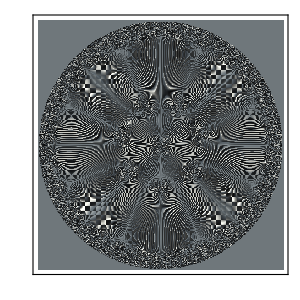
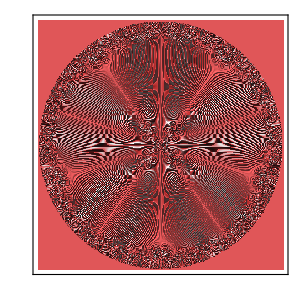

```mathematica
RPC1[m_,n_,s_,col_]:=With[{z=x+I y},ReliefPlot[Table[Cos[m*#]*Sin[#],
{x,##2},{y,##2}]&[If[Abs[z]>1.1 ,0,#]&@Arg[Sum[(z^n+10^(-3)z)^k!,{k,4}]],
-1.11,1.11,.005],ImageSize->s,ColorFunction->col]];
{RPC1[81,8,300,"GrayTones"],RPC1[64,5,300,"CherryTones"]}
```

```mathematica
RPC2[m_,n_,col_]:=With[{z=x+I y},ReliefPlot[Table[Cos[m*#],
{x,##2},{y,##2}]&[If[Abs[z]>1.15 ,0,#]&@Arg[Sum[(Sin[3z]*z)^k!,{k,4}]],
-1.2,1.2,.005],ImageSize->600,ColorFunction->col]];
RPC2[81,8,"BrassTones"]
```

-Graphics-

```mathematica
LFG[g_,n_,s_]:=Module[{edges,vertices,rtv},
edges=GraphData[g,"Edges"]; vertices=GraphData[g,"VertexCoordinates"];
rtv=Table[RotationTransform[j*Pi/n,{1.3,1.3}]/@vertices,{j,2n}];
lt[j_]:=Table[{rtv[[j]][[edges[[i,1]]]],
rtv[[j]][[edges[[i,2]]]]},{i,Length[edges]}];
Graphics[Table[Line[lt[j]],{j,2n}],ImageSize->s]]
{LFG["HundredTwentyCellGraph",3,300],LFG["DoubleStarSnark",9,300]}
```

{-Graphics-,-Graphics-}

```mathematica
LFG["SixHundredCellGraph",4,900]
```

-Graphics-

```mathematica
RTPT[poly_,n_,d_,p_,s_]:=Graphics3D[Table[Tube[RotationTransform[i*Pi/n,{0,0,1},
p]/@PolyhedronData[poly,"Edges","Coordinates"],d],{i,2n}],
Boxed->False,ViewPoint->Top,Background->Black,ImageSize->s];
{RTPT["EscherSolid",8,.02,{1.2,1.2,1.2},300],
RTPT["Dodecahedron",8,.07,{1,1,1},300]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
RTPT["GyroelongatedPentagonalBirotunda",4,.02,{1.3,1.3,1.3},600]
```

-Graphics3D-

```mathematica
AGRTP[m_,k_,s_,col_]:=Module[{ag},
ag=AdjacencyGraph[ExampleData[{"Matrix",ExampleData["Matrix"][[m,2]]},
"Matrix"]["PatternArray"],DirectedEdges->False,VertexSize->0];
CS[i_]:=ColorData[col][6Mod[i,Round[k/6]]/k];
RTAG[i_]:=RotationTransform[2i*Pi/k,{0,0}]/@ResourceFunction["VertexCoordinateList"][ag]//N;
Show[Table[GraphPlot[ag,VertexCoordinates->RTAG[i],EdgeStyle->CS[i]],{i,k}],ImageSize->s]]
{AGRTP[277,30,300,"CherryTones"],AGRTP[420,24,300,"CoffeeTones"]}
```

{-Graphics-,-Graphics-}

```mathematica
AGRTP[269,24,600,"CandyColors"]
```

-Graphics-

```mathematica
PPRT[n_,col_,l_,s_]:=Module[{a,b,c,d,u},
u=Pi/n; a=RandomInteger[{4,12}]; b=RandomInteger[{12,18}];
c=RandomInteger[{25,81}]; d=RandomInteger[{216,256}];
PF1[i_,t_]:=(a+.9Cos[b*t+u*i])(1+.1Cos[c*t+u*i]);
PF2[i_,t_]:=(1+.05Cos[d*t+u*i])(1+Sin[t+u*i]);
Show[Table[PolarPlot[PF1[i,t]*PF2[i,t],{t,-Pi,Pi},
PlotStyle->{Thickness[l],ColorData[col][.1Mod[i,Floor[n/2]]]}],
{i,2n+1}],Axes->False,ImageSize->s,PlotPoints->50]]
{PPRT[16,"BrightBands",.01,300],PPRT[4,"Rainbow",.001,300]}
```

{-Graphics-,-Graphics-}

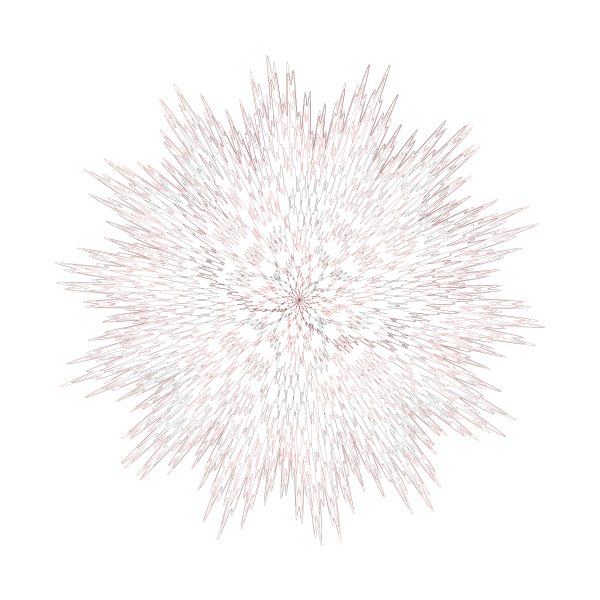

```mathematica
PPRT[8,"CherryTones",0,600]
```